# Mathematica Bootcamp: Step 3

전경원 박사

Machine Learning Research Engineer
(주)시정
ruddyscent@gmail.com

2021년 10월 18일 월요일

## Access to Lecture Materials

최신 자료는 아래 링크에서 내려받으실 수 있습니다.

https://github.com/ruddyscent/mathematica-bootcamp-2021

## References

체험하며 배우는 WOLFRAM MATHEMATICA
-Graphics-

Wolfram 언어 기초 입문
-Graphics-

Hands-on Start to Mathematica Online, Wolfram U
https://www.wolfram.com/wolfram-u/hands-on-start-to-mathematica-online/

## Wolfram Language

## Syntax Coloring

```mathematica
Expand[(x+1)^10]
```

Expandd[(x+1)^10]

Expand[

Expand[]]

```mathematica
Range[2,12,3]
```

Range[]

Range[2,12,3,1]

## 참값과 근삿값

718을 3으로 나눈값은?

```mathematica
718/3
```

718을 3으로 나누었을 때의 근삿값은?

```mathematica
N[718/3]
```

## List

```mathematica
{1,a,"가나다",-Graphics-,{}}
```

{1,a,가나다,-Graphics-,{}}

## 1부터 10까지의 자연수

```mathematica
{1,2,3,4,5,6,7,8,9,10}
```

Range[10]

Range[1, 10]

Range[1, 10, 3]

## 1부터 100까지 제곱수의 목록

```mathematica
{1^2,2^2,3^2,4^2,5^2,6^2,7^2,8^2,9^2,10^2}
```

Table[i^2,{i,10}]

Table[i^2,{i,0,10}]

Table[i^2,{i,0,10,2}]

Table[{i,i^2},{i,10}]

Table[π,10]

## 함수

```mathematica
f[x]
```

Sin[π]

전위 형식

```mathematica
f@x
```

Sin@π

후위 형식

```mathematica
x//f
```

π//Sin

## 합성함수.1c

```mathematica
g[f[x]]
```

Sin[Sin[π]]

전위 형식

```mathematica
g@f@x
```

Sin@Sin@π

후위 형식

```mathematica
x//f//g
```

x // Sin // Sin

## 순수함수

```mathematica
#^2&
```

Evaluate

```mathematica
#^2&[2]
```

4

전위 형식

```mathematica
#^2&@2
```

4

후위 형식

```mathematica
2//#^2&
```

## Rule

```mathematica
x->2
```

x^2/.x→2

Table[(x+i)^2,{i,10}]
%/.x→0

{f[x],g[x]}
%/.{f→(#^2&),g→(Sin[#]&)}

## Calculus

## Differentiation

전미분: Dt

```mathematica
Dt[a x^2 Sin[x],x]
```

TraditionalForm@HoldForm@Dt[a x^2 Sin[x],x]==Dt[a x^2 Sin[x],x]

편미분: D

```mathematica
D[a x^2 Sin[x],x]
```

HoldForm@D[a x^2 Sin[x],x]==D[a x^2 Sin[x],x]//TraditionalForm

고계 도함수

```mathematica
D[a x^2 Sin[x],{x,3}]
```

다변수 함수

∂/(∂y)∂/(∂x)(x^2 Cos[xy]+y^2 Sin[xy])

D[x^2 Cos[x y]+y^2 Sin[x y],x,y]

임의 함수 미분

```mathematica
D[g[x^2]g''[x],x]
```

D[g[x^2]g''[x],x]
%/.g→Sin

수식 정리

```mathematica
D[Sin[x]^10,{x,4}]
```

D[Sin[x]^10,{x,4}]
%//Simplify

## f(x)=x^3-2 x^2-4x+6의 도함수

도함수를 구하려면,

{f[x],f'[x],f''[x]}

{f[x],f'[x],f''[x]}
%/.f→(#^3-2#^2-4#+6&)

도함수의 그래프를 그리려면,

{f[x],f'[x],f''[x]}
%/.f→(#^3-2#^2-4#+6&)
Plot[%,{x,-3,3}]

{f[x],f'[x],f''[x]}
%/.f→(#^3-2#^2-4#+6&)
Plot[%,{x,-3,3},PlotLegends→{f[x],f'[x],f''[x]}]

도함수의 값을 표로 구하려면,

Table[{x,6-4 x-2 x^2+x^3,-4-4 x+3 x^2,-4+6 x},{x,-3,3}]//TableForm

## Limit

x가 1로 접글할 때, 1/x의 값을 구하려면,

```mathematica
Limit[1/x,x->1]
```

HoldForm@Limit[1/x,x→1]==Limit[1/x,x→1]

x가 무한히 커질 때, 1/x의 값을 구하려면,

```mathematica
Limit[1/x,x->Infinity]
```

```mathematica
Limit[1/x,x->∞]
```

좌극한, 우극한

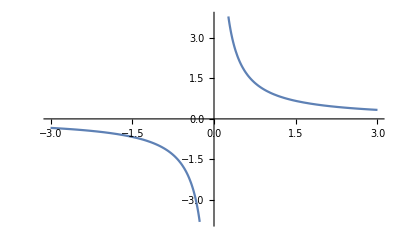

```mathematica
Plot[1/x,{x,-3,3}]
```

Limit[1/x,x→0,Direction→1]

Limit[1/x,x→0,Direction→-1]

Limit[1/x,x→0]

When Limit cannot compute a limit,

```mathematica
Limit[x^a,a->∞]
```

Limit[x^a,a→∞,Assumptions→Log[x]>0]

Limit[x^a,a→∞,Assumptions→x>1]

Limit[x^a,a→∞,Assumptions→x==1]

Limit[x^a,a→∞,Assumptions→0≤x<1]

## Indefinite Integration

## Definite Integration